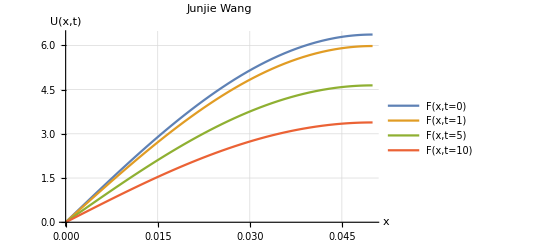

```mathematica
F[x_,t_]:=∑_(n=1)^1 {20/((2n-1)*Pi)*Sin[(2n-1)/0.1* Pi*x]*ⅇ^-(((2n-1)*Pi)^2*6.4*10^-3*t)}
Plot[{F[x,t=0],F[x,t=1],F[x,t=5],F[x,t=10]},{x,0,0.05},
AxesLabel-> {"x","U(x,t)"},
PlotLabel->"Junjie Wang",
PlotLegends->"Expressions",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

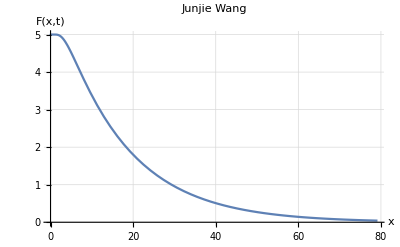

```mathematica
Plot[{F[x=0.05,t]},{t,0,79.16},
AxesLabel-> {"x","F(x,t)"},
PlotLabel->"Junjie Wang",
PlotLegends->"Expressions",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

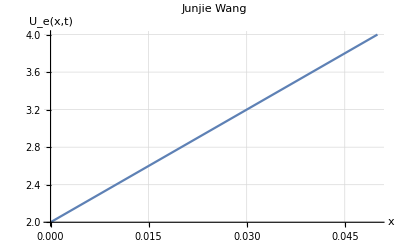

```mathematica
Plot[40x+2,{x,0,0.05},
AxesLabel-> {"x","U_e(x,t)"},
PlotLabel->"Junjie Wang",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```

General::munfl: Exp[-723.181] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-750.469] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-778.262] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

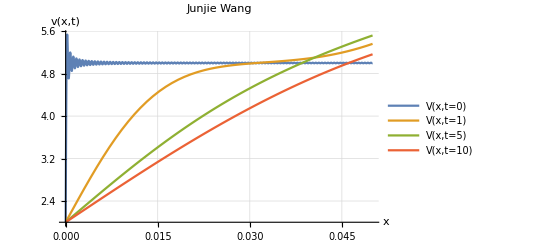

```mathematica
V[x_,t_]:=∑_(n=1)^200 {(12/((2n-1)*Pi)+0.4*40*(-1)^n/(((2n-1)*Pi)^2))*Sin[(2n-1)/0.1* Pi*x]*ⅇ^-(((2n-1)*Pi)^2*6.4*10^-3*t)}+40x+2
Plot[{V[x,t=0],V[x,t=1],V[x,t=5],V[x,t=10]},{x,0,0.05},
AxesLabel-> {"x","v(x,t)"},
PlotLabel->"Junjie Wang",
PlotLegends->"Expressions",
GridLines->Automatic,
BaseStyle->{FontSize-> 18}]
```